```mathematica
ClearAll["Global`*"]; Remove["Global`*"];
```

```mathematica
r={2,3};
p=Rationalize[{0.4,0.6}];
```

```mathematica
(* Analytic solution (2 r.v. only) *)
pmfX1[x_]=Binomial[x-1,r[[1]]-1] p[[1]]^r[[1]](1-p[[1]])^(x-r[[1]]);
pmfX2[x_]=Binomial[x-1,r[[2]]-1] p[[2]]^r[[2]](1-p[[2]])^(x-r[[2]]);
```

```mathematica
pmfZ[z_]=∑_(x=r[[1]])^(z-r[[2]]) pmfX1[x]pmfX2[z-x];
```

```mathematica
cdfZ[z_]=∑_(x=r[[1]]+r[[2]])^z pmfZ[x];
```

```mathematica
xs = Range[0,25];
```

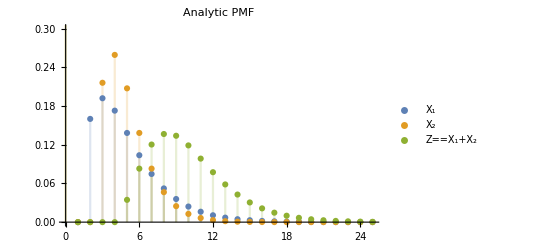

```mathematica
Style[{DiscretePlot[
{pmfX1[x],pmfX2[x],pmfZ[x]}, {x, xs},
PlotRange-> {0,0.3},
PlotLabel-> Style["Analytic PMF", FontWeight->Bold, FontColor-> Black],
PlotLegends-> {
ToExpression["X_1",TeXForm,HoldForm],
ToExpression["X_2",TeXForm,HoldForm],
ToExpression["Z=X_1+X_2",TeXForm,HoldForm]}]}, ImageSizeMultipliers->{1.5,1.5}]
```

```mathematica
(* Cumulant generating function and derivatives 1-4 *)
K[t_]=Total[r Log[p] + r t - r Log[1-(1-p)Exp[t]]];
K1[t_]=Total[r -((p-1)Exp[t]r)/((p-1)Exp[t]+1)];
K2[t_]=-Total[((p-1)Exp[t]r)/(p Exp[t]-Exp[t]+1)^2];
K3[t_]=Total[((p-1)Exp[t]r((p-1)Exp[t]-1))/((p-1)Exp[t]+1)^3];
K4[t_]=-Total[((p-1)Exp[t]r((p-1)^2Exp[2t]-4(p-1)Exp[t]+1))/((p-1)Exp[t]+1)^4];
```

```mathematica
(* First order S.P.A. of PMF *)
sHatULim = Min[Log[1/(1-p)]]; (* Upper bound of convergence strip of MGF *)
pmfSPA1[x_]=Module[
{sHat=NSolve[{K1[z]==x,z<sHatULim},z, Reals][[1,1,2]]},
1/(√(2π K2[sHat]))Exp[K[sHat]-x sHat]];
```

```mathematica
(* Compute integration of 1st order SPA PMF (~1) *)
∑_(x=6)^500 pmfSPA1[x]
```

0.99276

```mathematica
(* Second order S.P.A. of PMF *)
pmfSPA2[x_]=Module[
{sHat=NSolve[{K1[z]==x,z<sHatULim},z, Reals][[1, 1, 2]]},
 pmfSPA1[x](1+1/8(K4[sHat]/K2[sHat]^2)-5/24(K3[sHat]/K2[sHat]^(3/2))^2)];
```

```mathematica
(* Compute integration of 2nd order SPA PMF (~1) *)
∑_(x=6)^500 pmfSPA2[x]
```

0.964363

```mathematica
(* First order S.P.A. of CDF *)
cdfSPA1[x_]=Module[{x=x,x1=x+1,sHat,w,u,normPdfW,out}, (* increment x to account for strict inequality in SPA CDF (discrete) *)
sHat=NSolve[{K1[z]==x1,z<sHatULim},z, Reals][[1, 1, 2]];
w=Sign[sHat]Sqrt[2sHat x1-2K[sHat]];
u=(1-Exp[-sHat])Sqrt[K2[sHat]];
normPdfW=PDF[NormalDistribution[0,1],  w];
If[Abs[x1-K1[0]]<0.000001,
Evaluate[1/2(cdfSPA1[x-0.1]+cdfSPA1[x+0.1])], (* Removable singularity if X=E[X] - use linear interpolation *)
Evaluate[(CDF[NormalDistribution[0,1], w] + normPdfW(1/w-1/u))]]];
```

```mathematica
xs = Range[Total[r]+1,25];
```

```mathematica
trueValues = N[Map[pmfZ, xs]];
```

```mathematica
spa1Values = Map[pmfSPA1, xs];
```

```mathematica
spa2Values = Map[pmfSPA2, xs];
```

```mathematica
Grid[Transpose[{
Flatten[{"x", xs}],
Flatten[{"True", trueValues}],
Flatten[{"SPA 1st",spa1Values}],
Flatten[{"SPA 2nd",spa2Values}]}], Frame-> All]
```

x | True | SPA 1st | SPA 2nd
6 | 0.082944 | 0.0901188 | 0.0824519
7 | 0.120269 | 0.125693 | 0.120148
8 | 0.136581 | 0.140835 | 0.136561
9 | 0.133872 | 0.137072 | 0.133884
10 | 0.118909 | 0.121207 | 0.118915
11 | 0.0984601 | 0.100052 | 0.0984418
12 | 0.0773834 | 0.0784604 | 0.0773392
13 | 0.0584337 | 0.0591555 | 0.0583721
14 | 0.0427607 | 0.0432457 | 0.0426931
15 | 0.0305159 | 0.0308454 | 0.0304516
16 | 0.0213383 | 0.0215655 | 0.0212829
17 | 0.014673 | 0.0148319 | 0.0146286
18 | 0.00995014 | 0.0100623 | 0.00991658
19 | 0.00666903 | 0.00674861 | 0.00664472
20 | 0.00442583 | 0.00448228 | 0.00440883
21 | 0.00291242 | 0.0029523 | 0.00290087
22 | 0.00190262 | 0.00193062 | 0.00189495
23 | 0.00123512 | 0.00125462 | 0.00123013
24 | 0.000797405 | 0.00081087 | 0.000794209
25 | 0.000512329 | 0.000521545 | 0.000510309

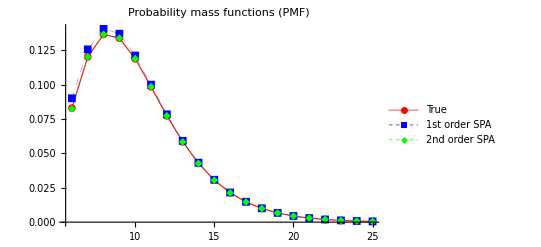

```mathematica
Style[{ListLinePlot[{Thread[{xs, trueValues}], Thread[{xs, spa1Values}], Thread[{xs, spa2Values}]}, PlotLegends ->{ "True", "1st order SPA" ,"2nd order SPA"}, 
PlotMarkers->{Automatic,8},
PlotStyle->{Directive[Red,Thickness[0.002]],Directive[Blue, Thickness[0.0005],Dashed],Directive[Green, Thickness[0.0005],Dashed]},
PlotLabel-> Style["Probability mass functions (PMF)", FontWeight->Bold, FontColor-> Black]]},ImageSizeMultipliers->{2,2}]
```

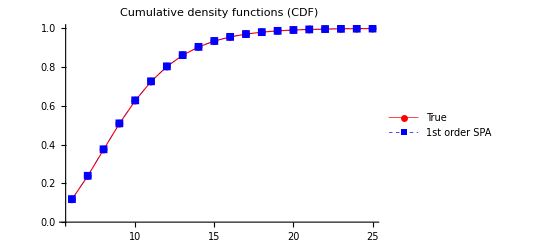

```mathematica
Style[{ListLinePlot[{Thread[{xs, Map[cdfZ, xs]}], Thread[{xs, Map[cdfSPA1, xs]}]}, PlotLegends ->{ "True", "1st order SPA" }, 
PlotMarkers->{Automatic,8},
PlotStyle->{Directive[Red,Thickness[0.002]],Directive[Blue, Thickness[0.0005],Dashed]},
PlotLabel-> Style["Cumulative density functions (CDF)", FontWeight->Bold, FontColor-> Black]]},ImageSizeMultipliers->{2,2}]
```

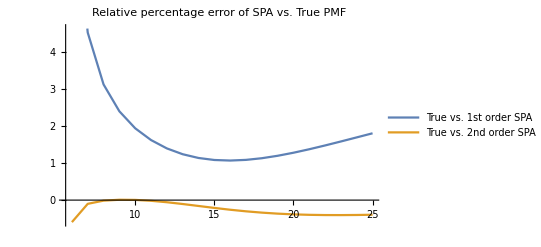

```mathematica
Style[{
ListLinePlot[{
Thread[{xs, 100(spa1Values - trueValues)/MapThread[Min,{trueValues, 1-trueValues}]}],
Thread[{xs, 100(spa2Values - trueValues)/MapThread[Min,{trueValues, 1-trueValues}]}]
},
PlotLegends-> {"True vs. 1st order SPA", "True vs. 2nd order SPA"},
PlotLabel-> Style["Relative percentage error of SPA vs. True PMF", FontWeight-> Bold, FontColor -> Black]]}, ImageSizeMultipliers->{2,2}]
```

```mathematica
Print["                  P(Z=8)     P(Z=12)    P(Z>8)     P(Z>12)"]
Print["True:            ", N[pmfZ[8]],        "   ", N[pmfZ[12]],       "   ", N[cdfZ[8]],       "   ", N[cdfZ[12]]]
Print["SPA 1st order:   ", N[pmfSPA1[8]], "   ", N[pmfSPA1[12]], "   ", N[cdfSPA1[8]],"   ", N[cdfSPA1[12]]]
Print["SPA 2nd order:   ",  N[pmfSPA2[8]], "   ", N[pmfSPA2[12]],"   ", "N/A", "        ", "N/A"]
```

P(Z=8)     P(Z=12)    P(Z>8)     P(Z>12)

True:            0.136581   0.0773834   0.374354   0.802978

SPA 1st order:   0.140835   0.0784604   0.375983   0.803958

SPA 2nd order:   0.136561   0.0773392   N/A        N/A